## Exercise 5: the evolution of aggressivity under limited dispersal

```mathematica
Clear["Global`*"]
```

### Relatedness in the moran model with n = 2

```mathematica
solr2 = Flatten@Solve[ r2 ==  1/n r2+(n-1)/n(1-m)(1/n+(n-1)/n r2),r2] /. n-> 2 //Simplify
```

{r2→(1-m)/(1+m)}

### Payoffs

```mathematica
PayoffFocal = y x (v/2-c)+ y (1-x)v + (1-y)x *0 + (1-y)(1-x)v/2  /. y-> zFocal/. x-> z1  ;
PayoffNeighbour = y x (v/2-c)+ y (1-x)v + (1-y)x *0 + (1-y)(1-x)v/2 /. y-> z1/. x-> zFocal ;
PayoffFResident= y x (v/2-c)+ y (1-x)v + (1-y)x *0 + (1-y)(1-x)v/2 /. y-> x  ;
```

### Individual fitness

```mathematica
w = 1/2 +1/2(1+δ PayoffFocal)((1-m)/(1/2(1-m)(1+δ PayoffFocal+1+δ PayoffNeighbour)+m (1+δ PayoffFResident))+m/(1+δ PayoffFResident)) ;
```

```mathematica
(* sanity check *)
w ==1/. zFocal-> x/.z1->x //Simplify
D[w,zFocal] + D[w,z1] + D[w,x] == 0  /. zFocal-> x/.z1->x //Simplify
```

True

True

### Selection gradient

```mathematica
D[w,zFocal] + r2 D[w,z1]  /. zFocal-> x/.z1->x  /. solr2//Simplify
Series[%,{δ,0,1}] //Normal 
S = % /. δ-> 1
```

(m (v+2 c (-2+m) x) δ)/((1+m) (2+v δ-2 c x^2 δ))

(m (v+2 c (-2+m) x) δ)/(2 (1+m))

(m (v+2 c (-2+m) x))/(2 (1+m))

```mathematica
equi = Flatten@Solve[S == 0,x]
```

{x→-v/(2 c (-2+m))}

```mathematica
-v/(2 c (-2+m)) == v/(2 c)1/(2-m) //Simplify
(* where v/(2 c) is the equilibrium in a well mixed population. This shows limited dispersal can reduce by half the probability of being aggressive *)
```

True

```mathematica
D[S,x] /. equi
(* which is always negative *)
```

(c (-2+m) m)/(1+m)

### Hessian

```mathematica
D[w,zFocal,zFocal] +2 r2 D[w,zFocal,z1] + r2 D[w,z1,z1]    /. zFocal-> x/.z1->x  /. solr2 /. equi//Simplify
Series[%,{δ,0,2}] //Normal  ;
H = % /. δ-> 1
```

-(4 c^2 (-2+m)^3 (-1+m) m δ)/((1+m) (-v^2 δ+2 c (-2+m)^2 (2+v δ)))

-(c (-2+m) (-1+m) m)/(1+m)-((-1+m) m (-8 c v+8 c m v-2 c m^2 v+v^2))/(4 (-2+m) (1+m))

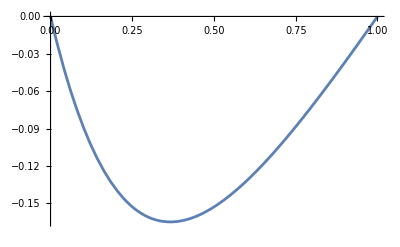

```mathematica
Plot[H /. v-> 1 /. c-> 1,{m,0,1}]
```

```mathematica
(* which shows that limited dispersal tends to make selection more stabilising. This is because kin selection tends to favour more even distribution of ressources. *)
```

## Exercise 6: the evolution of altruism for survival

```mathematica
Clear["Global`*"]
```

### Relatedness in the moran model with n = 2

```mathematica
solr2 = Flatten@Solve[ r2 ==  1/n r2+(n-1)/n(1-m)(1/n+(n-1)/n r2),r2] /. n->2 //Simplify
```

{r2→(1-m)/(1+m)}

### Fitness of focal with arbitrary survival and fecundity effects with n = 2

```mathematica
w = s[zFocal,z1]/(s[zFocal,z1]+s[z1,zFocal]) +1/2 f[zFocal,z1]((1-m)/(((f[zFocal,z1]+f[z1,zFocal])(1-m))/2+m f[x,x])+m/f[x,x]) ;
```

```mathematica
(* sanity check *)
w ==1/. zFocal-> x/.z1->x //Simplify
D[w,zFocal] + D[w,z1] + D[w,x] == 0  /. zFocal-> x/.z1->x //Simplify
```

True

True

### General selection gradient

```mathematica
S = D[w,zFocal]+r2 D[w,z1]/. zFocal-> x/.z1->x /. solr2 //FullSimplify ;
```

### Fecundity benefits and costs

```mathematica
f[x,x] S /. f->Function[{z1,z2},1+b z2 - c z1] /.s-> Function[{z1,z2},s]  // FullSimplify ; 
% ==((3-m) m)/(2 (1+m))(b (1-m)/(3-m)-c )//Simplify
```

True

### Survival benefits and costs

```mathematica
s[x,x] S /. f->Function[{z1,z2},f] /.s-> Function[{z1,z2},1+b z2 - c z1 ]  // FullSimplify ;
% ==m/(2 (1+m))(-b-c) //Simplify
```

True

```mathematica
(* so selection always acts against altruism here. This is because kin competition is very intense as you only compete against death within patches *)
```

### Survival costs and fecundity benefits

```mathematica
S /. f->Function[{z1,z2},1+b z2 ] /.s-> Function[{z1,z2},1- c z1 ]  // FullSimplify
```

(m (c+b (-1+m-c (-2+m) x)))/(2 (1+m) (1+b x) (-1+c x))

```mathematica
equi = Flatten@Solve[%==0,x]
```

{x→(-b+c+b m)/(b c (-2+m))}

```mathematica
D[S,x] /. f->Function[{z1,z2},1+b z2 ] /.s-> Function[{z1,z2},1- c z1 ]/. equi // FullSimplify
```

-(b^2 c^2 (-2+m)^3 m)/(2 (b+c)^2 (-1+m^2))

```mathematica
(* so now there exsists a stable intermediate level of altruism that increases with limited dispersal *)
```

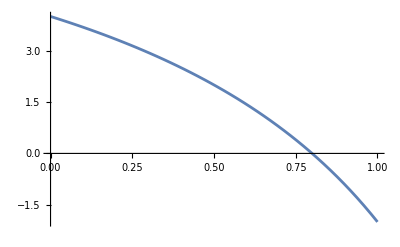

```mathematica
Plot[Evaluate[x/. equi/.c->.1 /.b->.5],{m,0,1},AxesOrigin->{0,0}]
```